```mathematica
Needs["DatabaseLink`"]
```

```mathematica
conn=OpenSQLConnection["dmkm_articles"]
```

SQLConnection[…]

```mathematica
ds1=SQLSelect[conn,"articles_1","MaxRows"->2000];
```

```mathematica
pair={ds1[[All,1]],ds1[[All,4]]}ᵀ;
```

```mathematica
relations=Table[ConditionalExpression[pair[[All,1]][[i]]<->pair[[All,1]][[j]],(pair[[All,2]][[i]]==pair[[All,2]][[j]])&&(pair[[All,1]][[i]]!=pair[[All,1]][[j]])&&(pair[[All,1]][[i]]≤pair[[All,1]][[j]])],{i,Length[pair]},{j,Length[pair]}];
```

```mathematica
DeleteDuplicates[DeleteCases[Flatten[relations],Undefined]]
```

{1<->2,1<->3,2<->3,4<->5,4<->6,4<->7,5<->6,5<->7,6<->7,8<->9,8<->10,9<->10,11<->12,11<->13,11<->14,36959,1991<->1993,1991<->1994,1991<->1995,1992<->1993,1992<->1994,1992<->1995,1993<->1994,1993<->1995,1994<->1995,1996<->1997,1996<->1998,1996<->1999,1997<->1998,1997<->1999,1998<->1999}
 |  |  |  |

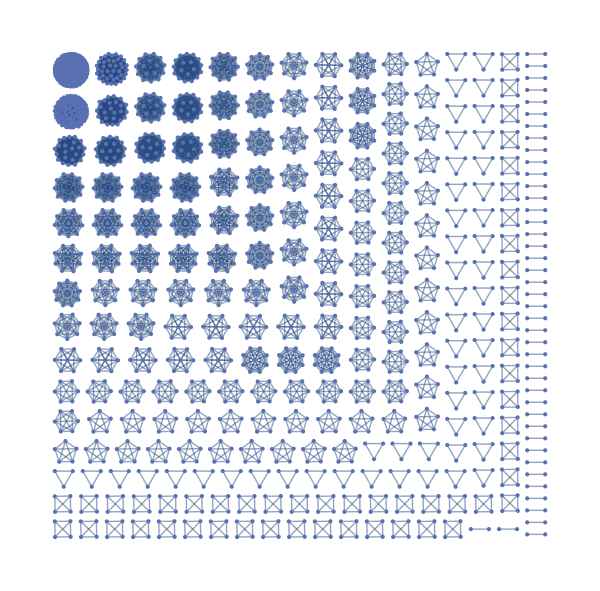

```mathematica
Graph[DeleteDuplicates[DeleteCases[Flatten[relations],Undefined]]]
```

```mathematica
ds2=SQLSelect[conn,"articles_authors","MaxRows"->2000]
```

{{0,0,Lukic M},{0,1,Houssin C},{0,2,Deharveng L},1994,{365,2,Pichardie D},{365,3,Turpin T},{366,0,Kadic M}}
 |  |  |  |

```mathematica
N[318591/475327]
```

0.670256

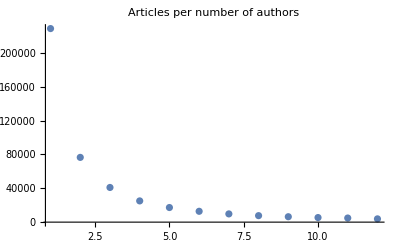

```mathematica
ListPlot[{{1,228782},
{2,76530},
{3,40972},
{4,25090},
{5,17267},
{6,12815},
{7,9733},
{8,7668},
{9,6401},
{10,5410},
{11,4860},
{12,3868}
},PlotRange->All,PlotLabel->"Articles per number of authors"]
```

```mathematica
ds3=SQLSelect[conn,"author_count"]
```

{{Banerjee S,458},{Brown DN,410},{Raoult D,389},{Martin A,385},475320,{Binder L,1},{Gross U,1},{Weig MS,1}}
 |  |  |  |

```mathematica
ListLogLinearPlot[ds3[[All,2]],PlotRange->All,PlotLabel->"Articles per unique author",Joined->False]
```

-Graphics-

```mathematica
ds4=SQLSelect[conn,"authors_per_article"];
```

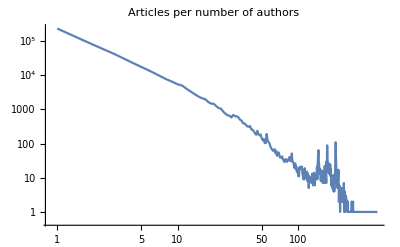

```mathematica
ListLogLogPlot[ds4,PlotRange->All,Joined->True,PlotLabel->"Articles per number of authors"]
```

```mathematica
N@Mean[ds3[[All,2]]]
```

4.89881